Possibility of Prolific Pair Production with High-Power Lasers

A. R. Bell, John G. Kirk, PRL 101, 200403 (2008)
Notebook: Óscar Amaro, December 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## Figure 1

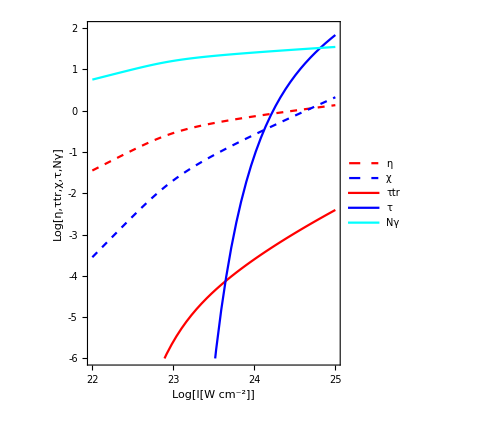

```mathematica
Clear[λμm,I24,η,a,χ,τtr,τ,αf,Nγ,γ,η5]
λμm=1;
αf=1/137;

η5[I24_]:=NSolve[I24==2.75 η^4+0.28 η/λμm,η,Reals][[2,1,2]](* eq 5, implicit relation *)

χ[I24_]:=0.42 η5[I24]^(3/2)Sqrt[I24 λμm](* after eq 6*)


τtr[I24_]:=0.06(I24 λμm^2)^(1/2)η5[I24]^(1/4)Exp[-8/(√(3η5[I24]))];(* in-text, before eq 7 *)

τ[I24_]:=12.8 (I24 λμm^2)Exp[-4/(3χ[I24])];(* in-text, after eq 7. this is the expression for χ<<1 *)

γ[I24_]:=(328Sqrt[η5[I24] λμm])/0.511;(* in-text, after eq 6 *)
Nγ[I24_]:=6.42 αf γ[I24] ;(* in-text, after eq 7 *)

Plot[{Log10[η5[10^(LogI-24)]],Log10[χ[10^(LogI-24)]],Log10[τtr[10^(LogI-24)]],Log10[τ[10^(LogI-24)]],Log10[Nγ[10^(LogI-24)]]},{LogI,22,25},PlotRange->{-6,2},FrameLabel->{"Log[I[W cm^-2]]","Log[η,τtr,χ,τ,Nγ]"},Frame->True,AspectRatio->1.2,ImageSize->Medium,PlotStyle->{{Red,Dashed},{Blue,Dashed},{Red},{Blue},Cyan},FrameTicks->{{{-6,-5,-4,-3,-2,-1,0,1,2},Automatic},{{22,23,24,25},Automatic}},PlotLegends->{"η","χ","τtr","τ","Nγ"}]//Quiet
```